```mathematica
rapp[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]/x2[[i,2]]},{i,1,Length[x1]}]
absrapp[x1_,x2_]:=Table[{x1[[i,1]],Abs[x1[[i,2]]/x2[[i,2]]]},{i,1,Length[x1]}]
mult[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]*x2[[i,2]]},{i,1,Length[x1]}]
sum[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]+x2[[i,2]]},{i,1,Length[x1]}]
sumlist[x1_]:=Table[{x1[[1,i,1]],x1[[1,i,2]]+x1[[2,i,2]]+x1[[3,i,2]]},{i,1,Length[x1[[1]]]}]
coeff[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]*c},{i,1,Length[x1]}]
sumconst[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]+c},{i,1,Length[x1]}]
diff[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]-x2[[i,2]]},{i,1,Length[x1]}]
joinbin[x_,n_]:=Map[{(Plus@@#)[[1]]/n,(Plus@@#)[[2]]}&,Partition[x,n]]
```

```mathematica
Estrai[filename_,histo_,namehisto_,nhisto_]:=Module[{file,positions,binning},
histo=.;
namehisto=.;
nhisto=.;
file=Import[filename,"Table"];
nhisto=0;
namehisto=Table[0,{j,1,100}];
positions=Table[0,{j,1,100}];
Do[
If[file[[i]]=={"<Histo>"}, 
nhisto=nhisto+1;
namehisto[[nhisto]]=file[[i+2]];
positions[[nhisto]]=i];
     ,{i,1,Length[file]}];
namehisto=Take[namehisto,nhisto];
positions=Take[positions,nhisto];
Do[(*Print[file[[ positions[[i]]+4 ]] ];*)binning[i]=file[[ positions[[i]]+4 ]];passo[i]=(binning[i][[3]]-binning[i][[2]])/binning[i][[1]],{i,1,nhisto}];
 Do[histo[i]=Table[{binning[i][[2]]+(j-1)passo[i],file[[positions[[i]]+18+j ,1 ]]},{j,0,binning[i][[1]]+1}],{i,1,nhisto}]
]
```

M(ttbar)>500 GeV con anche Pt(t)> 150 GeV e |etat|<2.5.

```mathematica
namerun="Mtt500_ptt150_eta2half"




(*namerun="hunderdkbiasto6withmax"*)
namerun="hunderdkbiasMINVto5withmax"
```

Mtt500_ptt150_eta2half

hunderdkbiasMINVto5withmax

```mathematica
(*namerunfix="hunderdkbiasto4"*)
```

```mathematica
namefolder="mupem_to_mupemttbar_2to4_noQED";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun(*fix*)<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun(*fix*)<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
etalnoQED=prova[5];
MllnoQED =prova[14];
MttnoQED =prova[15];
etatnoQED=prova[10];
pttnoQED =prova[8];
```

```mathematica
(*namerun="test180"*)
namefolder="ZZ_ttbar_2to2";
```

```mathematica
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muLePDF"<>"/tag_5_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muLePDF"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MttZZmuLePDF =prova[10];
etatZZmuLePDF=prova[6];
pttZZmuLePDF=prova[4];
```

```mathematica
namefolder="ZZ_ttbar_2to2";
NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muhalfLePDF"<>"/tag_5_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muhalfLePDF"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MttZZmuhalfLePDF =prova[10];
etatZZmuhalfLePDF=prova[6];
pttZZmuhalfLePDF=prova[4];

NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_muquarterLePDF"<>"/tag_5_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_muquarterLePDF"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MttZZmuquarterLePDF =prova[10];
etatZZmuquarterLePDF=prova[6];
pttZZmuquarterLePDF=prova[4];

(*NameH=.
NH=.
Estrai["/Users/pagani/mu-vbf/Davide2025/"<>namefolder<>"/HTML/"<>namerun<>"_ptmu"<>"/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_ptmu"<>"/MadAnalysis5job_0/Histograms/histos.saf",prova,NameH,NH]
MttZZptmu =prova[10];
etatZZptmu=prova[6];*)
```

```mathematica
plotlegend0={"2to4","2to4_noQED","2to4_onlyVBF"};
plotlegend={"2to4_noQED","ttbar Eva mu=sqrtshat","ttbar Eva mu=sqrtshat/2","ttbar Eva mu=sqrtshat/4", "ttbar Eva mu=sqrtshat a la LePDF", "ttbar Eva mu=sqrtshat/2 a la LePDF", "ttbar Eva mu=sqrtshat/4 a la LePDF"};
plotlegend2={"2to4_noQED", "ttbar Eva mu=sqrtshat a la LePDF", "ttbar Eva mu=sqrtshat/2 a la LePDF", "ttbar Eva mu=sqrtshat/4 a la LePDF"};
plotstyle0={Thick,Thick,Thick};
plotstyle={{Thick,Black},{Dashed,Blue},{Dashed,Red},{Dashed,Green}};
plotstyle2={{Thick,Black},{Dashed,Blue},{Dashed,Red},{Dashed,Green}};
```

```mathematica
NameH
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_PT},{6_ETA},{7_PT},{8_PT},{9_ETA},{10_M},{11_M},{12_M},{13_DELTAR}}

```mathematica
plotlabel="mu+ e- > t t~ at 10 TeV";
```

```mathematica
plotlegend0={"2to4","2to4_noQED","2to4_onlyVBF"};
plotlegend={"ME-noQED","EVA mu=m(tt) with only Log[mu/MV]","EVA mu=m(tt)/2 with only Log[mu/MV]","EVA mu=m(tt)/4 with only Log[mu/MV]", "EVA mu=m(tt)", "EVA mu=m(tt)/2", "EVA mu=m(tt)/4"};
plotlegend2={"ME-noQED", "EVA mu=m(tt)", "EVA mu=m(tt)/2", "EVA mu=m(tt)/4", "ttbar Eva mu=sqrtshat/4 a la LePDF"};
plotstyle0={Thick,Thick,Thick};
plotstyle={{Thick,Black},{Dashed,Blue},{Dashed,Red},{Dashed,Green}};
plotstyle2={{Thick,Black},{Dashed,Blue},{Dashed,Red},{Dashed,Green}};
```

```mathematica
plotlabel="mu+ e- > t t~ at 10 TeV, M(tt)>500 GeV, Pt(t)> 150 GeV,  |etat|<2.5";
```

Partition::pdep: Depth 1 requested in object with dimensions {}.

Part::partd: Part specification MttZZ⟦1⟧ is longer than depth of object.

Part::partd: Part specification MttZZ⟦2⟧ is longer than depth of object.

Part::partd: Part specification 10⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{MttZZ⟦1⟧/10,MttZZ⟦2⟧},{(10⟦1⟧)/10,10⟦2⟧}].

Partition::pdep: Depth 1 requested in object with dimensions {}.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{MttZZmuhalf⟦1⟧/10,MttZZmuhalf⟦2⟧},{(10⟦1⟧)/10,10⟦2⟧}].

Partition::pdep: Depth 1 requested in object with dimensions {}.

General::stop: Further output of Partition::pdep will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{MttZZmuquarter⟦1⟧/10,MttZZmuquarter⟦2⟧},{(10⟦1⟧)/10,10⟦2⟧}].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

ListLogPlot::lpn: {{{35.,Indeterminate},{135.,Indeterminate},{235.,Indeterminate},{335.,Indeterminate},{435.,Indeterminate},{535.,0.181912},{635.,0.536423},{735.,0.583197},{835.,0.512189},{935.,0.349141},«90»},{},{},{}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

ListLogPlot[{{{35.,0.},{135.,0.},{235.,0.},{335.,0.},{435.,0.},{535.,1.19951},{635.,1.70988},{735.,1.79176},{835.,1.66894},{935.,1.41785},{1035.,1.13946},{1135.,0.967521},{1235.,0.806495},{1335.,0.626364},{1435.,0.581332},{1535.,0.461534},{1635.,0.397451},{1735.,0.354583},{1835.,0.288703},{1935.,0.264527},{2035.,0.21021},{2135.,0.185151},{2235.,0.161087},{2335.,0.139731},{2435.,0.11594},{2535.,0.105693},{2635.,0.0853086},{2735.,0.0799496},{2835.,0.0713831},{2935.,0.0579723},{3035.,0.0550779},{3135.,0.0457551},{3235.,0.0404027},{3335.,0.0383515},{3435.,0.0331091},{3535.,0.0299175},{3635.,0.0259814},{3735.,0.0234785},{3835.,0.0205583},{3935.,0.0190663},{4035.,0.0166481},{4135.,0.014838},{4235.,0.013129},{4335.,0.0117382},{4435.,0.0105844},{4535.,0.00963538},{4635.,0.00851767},{4735.,0.0077698},{4835.,0.00694764},{4935.,0.00625627},{5035.,0.0054263},{5135.,0.00471216},{5235.,0.00466778},{5335.,0.00408262},{5435.,0.00367809},{5535.,0.00331983},{5635.,0.00309375},{5735.,0.00259558},{5835.,0.00235498},{5935.,0.00216652},{6035.,0.00208974},{6135.,0.0018349},{6235.,0.00160616},{6335.,0.00145245},{6435.,0.00133664},{6535.,0.00118904},{6635.,0.00106734},{6735.,0.000952597},{6835.,0.000846778},{6935.,0.000775348},{7035.,0.000735386},{7135.,0.000592516},{7235.,0.000563578},{7335.,0.000470221},{7435.,0.000405264},{7535.,0.000397871},{7635.,0.000353824},{7735.,0.000287957},{7835.,0.000264173},{7935.,0.000229514},{8035.,0.000205261},{8135.,0.000181955},{8235.,0.000155858},{8335.,0.000141123},{8435.,0.0001078},{8535.,0.000107242},{8635.,0.0000847139},{8735.,0.0000738899},{8835.,0.0000601472},{8935.,0.0000501818},{9035.,0.0000383431},{9135.,0.0000383614},{9235.,0.0000266513},{9335.,0.0000185712},{9435.,0.0000131519},{9535.,0.0000114524},{9635.,5.85406×10^-6},{9735.,3.1978×10^-6},{9835.,1.46668×10^-6},{9935.,3.22262×10^-7}},Partition[{MttZZ⟦1⟧/10,MttZZ⟦2⟧},{(10⟦1⟧)/10,10⟦2⟧}],Partition[{MttZZmuhalf⟦1⟧/10,MttZZmuhalf⟦2⟧},{(10⟦1⟧)/10,10⟦2⟧}],Partition[{MttZZmuquarter⟦1⟧/10,MttZZmuquarter⟦2⟧},{(10⟦1⟧)/10,10⟦2⟧}]},InterpolationOrder→0,Joined→True,PlotLegends→{ME-noQED,EVA mu=m(tt) with only Log[mu/MV],EVA mu=m(tt)/2 with only Log[mu/MV],EVA mu=m(tt)/4 with only Log[mu/MV],EVA mu=m(tt),EVA mu=m(tt)/2,EVA mu=m(tt)/4},PlotStyle→{{Thickness[Large],GrayLevel[0]},{Dashing[{Small,Small}],RGBColor[0, 0, 1]},{Dashing[{Small,Small}],RGBColor[1, 0, 0]},{Dashing[{Small,Small}],RGBColor[0, 1, 0]}},PlotLabel→mu+ e- > t t~ at 10 TeV, M(tt)>500 GeV, Pt(t)> 150 GeV,  |etat|<2.5,AxesLabel→{m(tt),Events at 10 fb^-1},BaseStyle→Directive[17,FontFamily→Times],ImageSize→550]

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

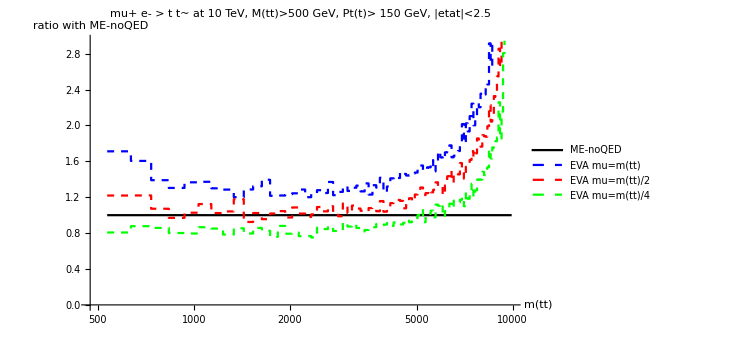

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

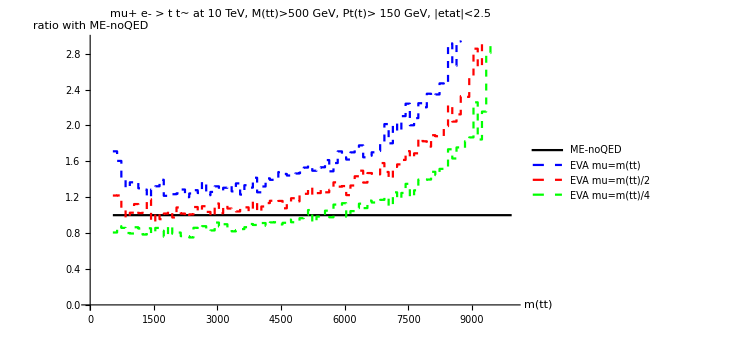

ListLogPlot::lpn: {{{-10.5,Indeterminate},{-10.,Indeterminate},{-9.5,Indeterminate},{-9.,Indeterminate},{-8.5,Indeterminate},{-8.,Indeterminate},{-7.5,Indeterminate},{-7.,Indeterminate},{-6.5,Indeterminate},{-6.,Indeterminate},«32»},{},{},{}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

ListLogPlot[{{{-10.5,0.},{-10.,0.},{-9.5,0.},{-9.,0.},{-8.5,0.},{-8.,0.},{-7.5,0.},{-7.,0.},{-6.5,0.},{-6.,0.},{-5.5,0.},{-5.,0.},{-4.5,0.},{-4.,0.},{-3.5,0.},{-3.,0.293553},{-2.5,0.982297},{-2.,1.27272},{-1.5,1.60368},{-1.,1.70535},{-0.5,1.84528},{0.,1.78386},{0.5,1.77427},{1.,1.63122},{1.5,1.25887},{2.,0.970786},{2.5,0.259092},{3.,0.},{3.5,0.},{4.,0.},{4.5,0.},{5.,0.},{5.5,0.},{6.,0.},{6.5,0.},{7.,0.},{7.5,0.},{8.,0.},{8.5,0.},{9.,0.},{9.5,0.},{10.,0.}},etatZZ,etatZZmuhalf,etatZZmuquarter},InterpolationOrder→0,Joined→True,PlotLegends→{ME-noQED,EVA mu=m(tt) with only Log[mu/MV],EVA mu=m(tt)/2 with only Log[mu/MV],EVA mu=m(tt)/4 with only Log[mu/MV],EVA mu=m(tt),EVA mu=m(tt)/2,EVA mu=m(tt)/4},PlotStyle→{{Thickness[Large],GrayLevel[0]},{Dashing[{Small,Small}],RGBColor[0, 0, 1]},{Dashing[{Small,Small}],RGBColor[1, 0, 0]},{Dashing[{Small,Small}],RGBColor[0, 1, 0]}},PlotLabel→mu+ e- > t t~ at 10 TeV, M(tt)>500 GeV, Pt(t)> 150 GeV,  |etat|<2.5,AxesLabel→{eta(t),Events at 10 fb^-1},BaseStyle→Directive[17,FontFamily→Times],ImageSize→550]

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

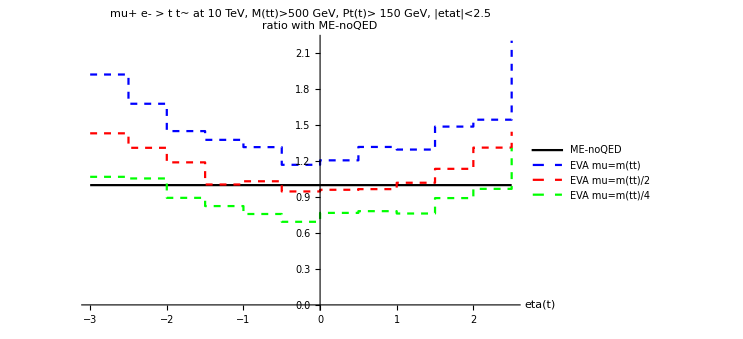

Partition::pdep: Depth 1 requested in object with dimensions {}.

Part::partd: Part specification pttZZ⟦1⟧ is longer than depth of object.

Part::partd: Part specification pttZZ⟦2⟧ is longer than depth of object.

Part::partd: Part specification 10⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{pttZZ⟦1⟧/10,pttZZ⟦2⟧},{(10⟦1⟧)/10,10⟦2⟧}].

Partition::pdep: Depth 1 requested in object with dimensions {}.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{pttZZmuhalf⟦1⟧/10,pttZZmuhalf⟦2⟧},{(10⟦1⟧)/10,10⟦2⟧}].

Partition::pdep: Depth 1 requested in object with dimensions {}.

General::stop: Further output of Partition::pdep will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{pttZZmuquarter⟦1⟧/10,pttZZmuquarter⟦2⟧},{(10⟦1⟧)/10,10⟦2⟧}].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

ListLogPlot::lpn: {{{35.,Indeterminate},{135.,0.429062},{235.,1.44761},{335.,1.18804},{435.,0.74863},{535.,0.285497},{635.,-0.21036},{735.,-0.57598},{835.,-0.907356},{935.,-1.29428},«90»},{},{},{}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

ListLogPlot[{{{35.,0.},{135.,1.53582},{235.,4.25293},{335.,3.28063},{435.,2.1141},{535.,1.33042},{635.,0.810292},{735.,0.562154},{835.,0.40359},{935.,0.274096},{1035.,0.196279},{1135.,0.159234},{1235.,0.104468},{1335.,0.0702766},{1435.,0.0754208},{1535.,0.0517476},{1635.,0.0353583},{1735.,0.0245761},{1835.,0.0265428},{1935.,0.0151377},{2035.,0.00968096},{2135.,0.00819459},{2235.,0.00689184},{2335.,0.00671977},{2435.,0.00844409},{2535.,0.00492903},{2635.,0.00295396},{2735.,0.00203381},{2835.,0.00159425},{2935.,0.00112851},{3035.,0.000904276},{3135.,0.000899614},{3235.,0.00081889},{3335.,0.000434245},{3435.,0.000925931},{3535.,0.000251023},{3635.,0.000289445},{3735.,0.000254034},{3835.,0.000137908},{3935.,0.000144171},{4035.,0.0000988389},{4135.,0.0000572275},{4235.,0.000039241},{4335.,0.0000219174},{4435.,0.0000139659},{4535.,0.0000104498},{4635.,0.000018453},{4735.,2.3007×10^-6},{4835.,2.59214×10^-6},{4935.,1.06545×10^-7},{5035.,0.},{5135.,0.},{5235.,0.},{5335.,0.},{5435.,0.},{5535.,0.},{5635.,0.},{5735.,0.},{5835.,0.},{5935.,0.},{6035.,0.},{6135.,0.},{6235.,0.},{6335.,0.},{6435.,0.},{6535.,0.},{6635.,0.},{6735.,0.},{6835.,0.},{6935.,0.},{7035.,0.},{7135.,0.},{7235.,0.},{7335.,0.},{7435.,0.},{7535.,0.},{7635.,0.},{7735.,0.},{7835.,0.},{7935.,0.},{8035.,0.},{8135.,0.},{8235.,0.},{8335.,0.},{8435.,0.},{8535.,0.},{8635.,0.},{8735.,0.},{8835.,0.},{8935.,0.},{9035.,0.},{9135.,0.},{9235.,0.},{9335.,0.},{9435.,0.},{9535.,0.},{9635.,0.},{9735.,0.},{9835.,0.},{9935.,0.}},Partition[{pttZZ⟦1⟧/10,pttZZ⟦2⟧},{(10⟦1⟧)/10,10⟦2⟧}],Partition[{pttZZmuhalf⟦1⟧/10,pttZZmuhalf⟦2⟧},{(10⟦1⟧)/10,10⟦2⟧}],Partition[{pttZZmuquarter⟦1⟧/10,pttZZmuquarter⟦2⟧},{(10⟦1⟧)/10,10⟦2⟧}]},InterpolationOrder→0,Joined→True,PlotLegends→{ME-noQED,EVA mu=m(tt) with only Log[mu/MV],EVA mu=m(tt)/2 with only Log[mu/MV],EVA mu=m(tt)/4 with only Log[mu/MV],EVA mu=m(tt),EVA mu=m(tt)/2,EVA mu=m(tt)/4},PlotStyle→{{Thickness[Large],GrayLevel[0]},{Dashing[{Small,Small}],RGBColor[0, 0, 1]},{Dashing[{Small,Small}],RGBColor[1, 0, 0]},{Dashing[{Small,Small}],RGBColor[0, 1, 0]}},PlotLabel→mu+ e- > t t~ at 10 TeV, M(tt)>500 GeV, Pt(t)> 150 GeV,  |etat|<2.5,AxesLabel→{pt(t),Events at 10 fb^-1},BaseStyle→Directive[17,FontFamily→Times],ImageSize→550]

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

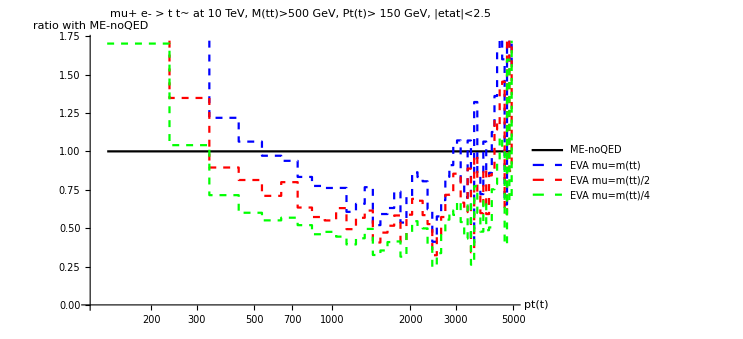

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

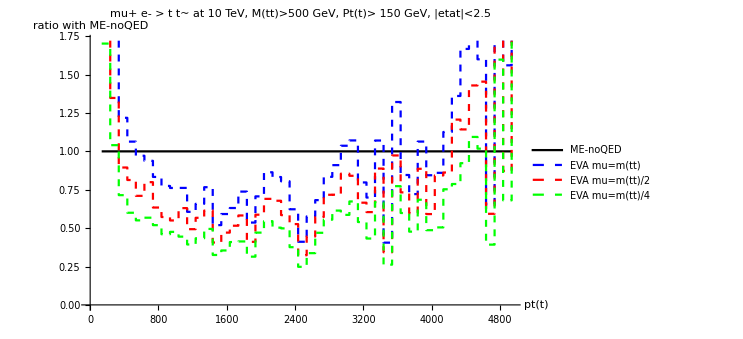

10TeVcuts_datforMarco/

```mathematica
plotmtt=ListLogPlot[{joinbin[MttnoQED,10],joinbin[MttZZmuLePDF,10],joinbin[MttZZmuhalfLePDF,10],joinbin[MttZZmuquarterLePDF,10]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(tt)","Events at 10 fb^-1"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 

plotmttratio2=ListLogLinearPlot[{rapp[joinbin[MttnoQED,10],joinbin[MttnoQED,10]],rapp[joinbin[MttZZmuLePDF,10],joinbin[MttnoQED,10]],rapp[joinbin[MttZZmuhalfLePDF,10],joinbin[MttnoQED,10]],rapp[joinbin[MttZZmuquarterLePDF,10],joinbin[MttnoQED,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend2,PlotStyle->plotstyle2,PlotLabel->plotlabel,AxesLabel->{"m(tt)","ratio with ME-noQED"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 

plotmttratio2b=ListPlot[{rapp[joinbin[MttnoQED,10],joinbin[MttnoQED,10]],rapp[joinbin[MttZZmuLePDF,10],joinbin[MttnoQED,10]],rapp[joinbin[MttZZmuhalfLePDF,10],joinbin[MttnoQED,10]],rapp[joinbin[MttZZmuquarterLePDF,10],joinbin[MttnoQED,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend2,PlotStyle->plotstyle2,PlotLabel->plotlabel,AxesLabel->{"m(tt)","ratio with ME-noQED"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 






plotetat=ListLogPlot[{etatnoQED,etatZZmuLePDF,etatZZmuhalfLePDF,etatZZmuquarterLePDF},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"eta(t)","Events at 10 fb^-1"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 


plotetatratio2=ListPlot[{rapp[joinbin[etatnoQED,1],joinbin[etatnoQED,1]],rapp[joinbin[etatZZmuLePDF,1],joinbin[etatnoQED,1]],rapp[joinbin[etatZZmuhalfLePDF,1],joinbin[etatnoQED,1]],rapp[joinbin[etatZZmuquarterLePDF,1],joinbin[etatnoQED,1]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend2,PlotStyle->plotstyle2,PlotLabel->plotlabel,AxesLabel->{"eta(t)","ratio with ME-noQED"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 



plotptt=ListLogPlot[{joinbin[pttnoQED,10],joinbin[pttZZmuLePDF,10],joinbin[pttZZmuhalfLePDF,10],joinbin[pttZZmuquarterLePDF,10]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"pt(t)","Events at 10 fb^-1"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 


plotpttratio2=ListLogLinearPlot[{rapp[joinbin[pttnoQED,10],joinbin[pttnoQED,10]],rapp[joinbin[pttZZmuLePDF,10],joinbin[pttnoQED,10]],rapp[joinbin[pttZZmuhalfLePDF,10],joinbin[pttnoQED,10]],rapp[joinbin[pttZZmuquarterLePDF,10],joinbin[pttnoQED,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend2,PlotStyle->plotstyle2,PlotLabel->plotlabel,AxesLabel->{"pt(t)","ratio with ME-noQED"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 

plotpttratio2b=ListPlot[{rapp[joinbin[pttnoQED,10],joinbin[pttnoQED,10]],rapp[joinbin[pttZZmuLePDF,10],joinbin[pttnoQED,10]],rapp[joinbin[pttZZmuhalfLePDF,10],joinbin[pttnoQED,10]],rapp[joinbin[pttZZmuquarterLePDF,10],joinbin[pttnoQED,10]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend2,PlotStyle->plotstyle2,PlotLabel->plotlabel,AxesLabel->{"pt(t)","ratio with ME-noQED"},BaseStyle->Directive[17,FontFamily->"Times"],ImageSize->550] 




dir="/Users/pagani/mu-vbf/Davide2025/Notebooks/Plot_and_dats_forpaper/ZZ_tt/10TeVcuts/"<>ToString[namerun]<>"/";
Export[dir<>"plotmtt.pdf",plotmtt];
Export[dir<>"plotmttratio2.pdf",plotmttratio2];
Export[dir<>"plotmttratio2b.pdf",plotmttratio2b];

Export[dir<>"plotetat.pdf",plotetat];
Export[dir<>"plotetatratio2.pdf",plotetatratio2];

Export[dir<>"plotptt.pdf",plotptt];
Export[dir<>"plotpttratio2.pdf",plotpttratio2];
Export[dir<>"plotpttratio2b.pdf",plotpttratio2b];



binnabene[x_]:=Module[{binw},binw=x[[2,1]]-x[[1,1]];Table[{x[[i,1]],x[[i,1]]+binw,x[[i,2]]},{i,1,Length[x]}]];
run="10TeVcuts_datforMarco/"
Export[dir<>"etatnoQED.dat",binnabene[etatnoQED]];
Export[dir<>"etatmuquarterLePDF.dat",binnabene[etatZZmuquarterLePDF]];
Export[dir<>"etatmuhalfLePDF.dat",binnabene[etatZZmuhalfLePDF]];
Export[dir<>"etatmuLePDF.dat",binnabene[etatZZmuLePDF]];
Export[dir<>"pttnoQED.dat",binnabene[pttnoQED]];
Export[dir<>"pttmuquarterLePDF.dat",binnabene[pttZZmuquarterLePDF]];
Export[dir<>"pttmuhalfLePDF.dat",binnabene[pttZZmuhalfLePDF]];
Export[dir<>"pttmuLePDF.dat",binnabene[pttZZmuLePDF]];
Export[dir<>"mttnoQED.dat",binnabene[MttnoQED]];
Export[dir<>"mttmuquarterLePDF.dat",binnabene[MttZZmuquarterLePDF]];
Export[dir<>"mttmuhalfLePDF.dat",binnabene[MttZZmuhalfLePDF]];
Export[dir<>"mttmuLePDF.dat",binnabene[MttZZmuLePDF]];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Partition::pdep: Depth 1 requested in object with dimensions {}.

Part::partd: Part specification MttZZ⟦1⟧ is longer than depth of object.

Part::partd: Part specification MttZZ⟦2⟧ is longer than depth of object.

Part::partd: Part specification 20⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{MttZZ⟦1⟧/20,MttZZ⟦2⟧},{(20⟦1⟧)/20,20⟦2⟧}].

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Partition::pdep: Depth 1 requested in object with dimensions {}.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{MttZZmuhalf⟦1⟧/20,MttZZmuhalf⟦2⟧},{(20⟦1⟧)/20,20⟦2⟧}].

Partition::pdep: Depth 1 requested in object with dimensions {}.

General::stop: Further output of Partition::pdep will be suppressed during this calculation.

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{MttZZmuquarter⟦1⟧/20,MttZZmuquarter⟦2⟧},{(20⟦1⟧)/20,20⟦2⟧}].

General::stop: Further output of Partition::ilsmp will be suppressed during this calculation.

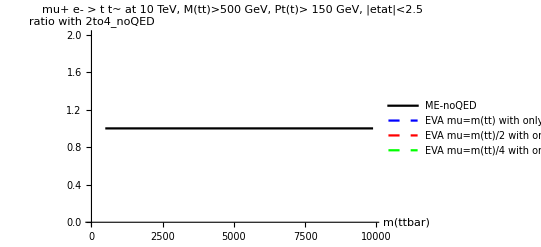

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

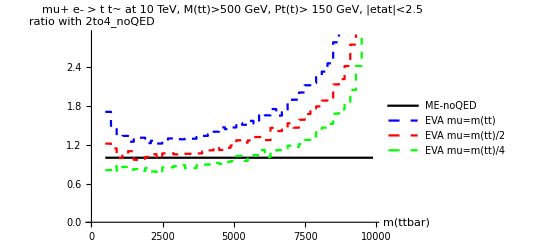

```mathematica
rebinning=20;
ListPlot[{rapp[joinbin[MttnoQED,rebinning],joinbin[MttnoQED,rebinning]],rapp[joinbin[MttZZ,rebinning],joinbin[MttnoQED,rebinning]],rapp[joinbin[MttZZmuhalf,rebinning],joinbin[MttnoQED,rebinning]],rapp[joinbin[MttZZmuquarter,rebinning],joinbin[MttnoQED,rebinning]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend,PlotStyle->plotstyle,PlotLabel->plotlabel,AxesLabel->{"m(ttbar)","ratio with 2to4_noQED"}] 

ListPlot[{rapp[joinbin[MttnoQED,rebinning],joinbin[MttnoQED,rebinning]],rapp[joinbin[MttZZmuLePDF,rebinning],joinbin[MttnoQED,rebinning]],rapp[joinbin[MttZZmuhalfLePDF,rebinning],joinbin[MttnoQED,rebinning]],rapp[joinbin[MttZZmuquarterLePDF,rebinning],joinbin[MttnoQED,rebinning]]},InterpolationOrder->0,Joined->True,PlotLegends->plotlegend2,PlotStyle->plotstyle2,PlotLabel->plotlabel,AxesLabel->{"m(ttbar)","ratio with 2to4_noQED"}]
```